# Benard Cell analysis

## Schema

A simple Benard cell can be represented by three parts: the heater H, the cooler C much bigger than the system of interest S which is placed in between the two. The analysis usually goes along this lines: if the temperature difference between the heater and the cooler ΔT=T_H-T_C is small then the heat transfer occurs by diffusion, however if the temperature difference a critical point a second mechanism, convection, engages in heat transfer.

-Graphics-

Benard cell schema; the heater and cooler are in thermal equilibrium.

## Analysis

We’ll analyze it from the perspective of internal entropy produced (i) and external entropy transferred (e) to the system of interest S. Of course entropy change of the system ⅆ S_S would be the sum of those two:

(ⅆ S_S)/ⅆt=(ⅆ S_i)/ⅆt+(ⅆ S_e)/ⅆt

In our analysis we’ll limit ourselves to the scenario of a stable state in which the same amount of heat that goes in also goes out. In other words Q_C=-Q_H and we get

ⅆ S_e=(ⅆ Q_H)/T_H+(ⅆ Q_C)/T_C=ⅆQ_H(1/T_H-1/T_C)=ⅆQ_H((T_C-T_H)/(T_H T_C))<0

Therefore the process transfers some of the entropy outside the system. However, since we require a stable state ⅆ S_S=0 it leads us to the conclusion that ⅆ S_i=-ⅆ S_e>0, so in a sense we could say that the rate of internal entropy production ⅆ S_i is a function of the entropy inflow ⅆ S_e. Moreover the entropy gets lowered by negative inflow of entropy, so S-S_0<0, where S_0=S(t=0).

If we now consider a scenario in which j_e=(ⅆ S_e)/ⅆt was non–zero for some time and then turned off, then by Tylor expansion

(ⅆ S_i)/ⅆt=j_i(S)=j_i(S_0)+(S-S_0)C_1+𝒪(S^2)

and noticing that j_i(S_0)=0 by definition (if the inflow of entropy is null, then the system stays in equilibrium) and therefore C_1 has to be negative since j_i(S)>0 and S-S_0<0.
Further we rewrite the equation with C_1=-1/τ (τ positive)

(ⅆ S_i)/ⅆt=j_i(S_i)=(S_0-S_i)/τ+𝒪(S^2)

and solve this equation:

```mathematica
DSolve[y'[t]==(y0-y[t])/τ,y[t],t]
```

{{y[t]→y0+ⅇ^(-t/τ) C[1]}}

S_i(t)=S_0(1-ⅇ^(-t/τ))+S_1 ⅇ^(-t/τ)

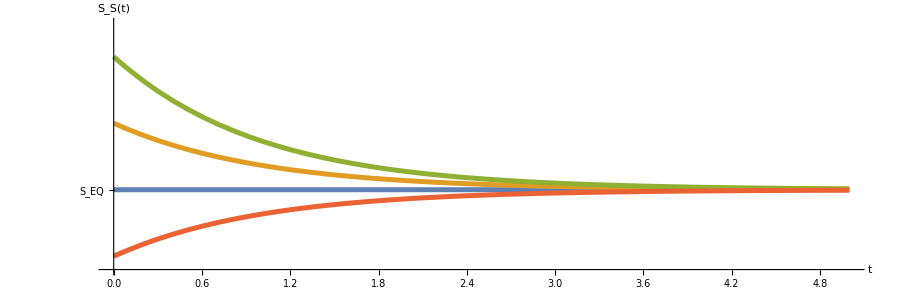

```mathematica
Plot[{2,3 ⅇ^(-t/τ) +2(1-ⅇ^(-t/τ))/.{τ->1},4 ⅇ^(-t/τ) +2(1-ⅇ^(-t/τ))/.{τ->1},1 ⅇ^(-t/τ) +2(1-ⅇ^(-t/τ))/.{τ->1} },{t,0,5},AxesLabel->{Style["t",FontSize->26],Style["S_S(t)",FontSize->26]},Ticks->{None,{{2,Style["S_EQ",FontSize->22]}}},PlotRange->{{0,5},{0.8,4.5}},ImageSize->{900,300}, AspectRatio->1/3,PlotStyle->Directive[Thickness[0.004]],AxesStyle->Directive[Thick,Black,FontSize->22,Arrowheads[{0.0,0.03}]]]
```

```mathematica
-Sum[1/2 Log[2,1/2],{i,1,2}]
```

1

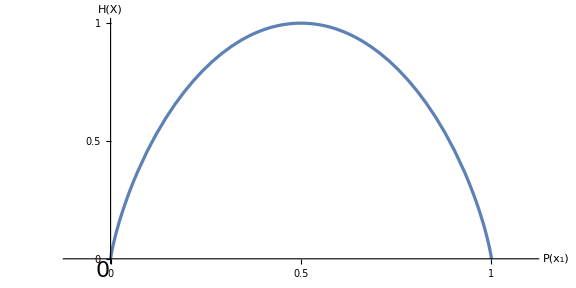

```mathematica
Plot[-p Log[2,p]-(1-p)Log[2,1-p],{p,-0.1,1.1},AxesLabel->{Style["P(x_1)",FontSize->22],Style["H(X)",FontSize->22]},AspectRatio->1/2,ImageSize->Large,Ticks->{{0,.5,1},{0,0.5,1}},Epilog->Text[Style[0,FontSize->22],Offset[{-8,-12},{0,0}]],PlotRangePadding->0.1,AxesStyle->Directive[Thick,Black,FontSize->22,Arrowheads[{0.0,0.04}]],PlotStyle->Directive[Thickness[0.004]]]
```

Therefore the system returns to equilibrium as expected

However if consider an equation in which j_e≠0 then we get a different solution

```mathematica
DSolve[y'[t]==je+(y0-y[t])/τ,y[t],t]
```

{{y[t]→y0+je τ+ⅇ^(-t/τ) C[1]}}

S_i(t)=S_0+j_e τ(1-ⅇ^(-t/τ))

The entropy smoothly lowers to minimum entropy

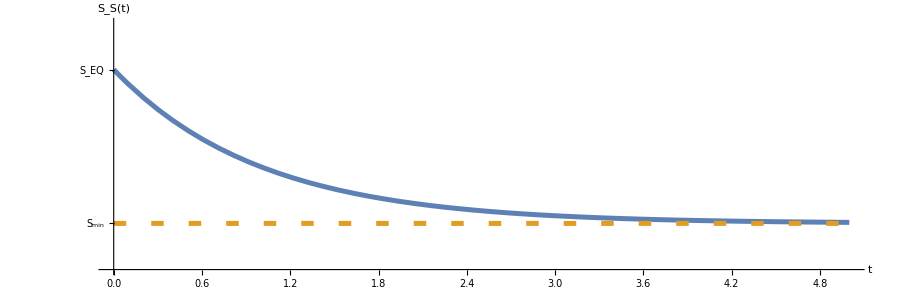

```mathematica
Plot[{y0+je τ+ⅇ^(-t/τ) /.{τ->1,y0->2,je->1},3},{t,0,5},PlotRange->{{0,5},{2.7,4.3}},AxesLabel->{Style["t",FontSize->22],Style["S_S(t)",FontSize->22]},Ticks->{None,{{3,Style["S_min",FontSize->22]},{4.0,Style["S_EQ",FontSize->22]}}},PlotRange->Full,ImageSize->{900,300}, AspectRatio->1/3,PlotStyle->{{Thickness[0.004]},{Thickness[0.004],Dashing[{0.01,0.02}]}},AxesStyle->Directive[Thick,Black,FontSize->22,Arrowheads[{0.0,0.03}]]]
```

```mathematica
Integrate[Exp[-x]/(1+Exp[-x]),{x,0,∞}]
```

Log[2]

and we see that j_i→j_max=(S_0-S_min)/τ=-j_e.

The Benard cell doesn’t store energy, hence internal energy stays constant, but since as we saw entropy get’s minimized at steady state that means that free energy, defined by

F=U-TS

gets maximized. This free energy again allows us to perform work which in this case is visualized in the circular, convective motions of the fluid.

Now we may make a weak association with information – since erase of information is associated with entropy production (due to Landauer), then we can say that at steady–state the amount of information stays constant, even though the it’s inflow is non–zero (negative ⅆ S_e) it get’s immediately erased by the non–zero internal entropy production (positive ⅆ S_i)

[Calculation of complexity]

Problem jaki widzę, to to, że te równania są spełnione równania są spełnione również podczas dyfuzji, a więc nie mówią nam nic specjalnego o konwekcji i dlatego człon ⅆ S_i/ⅆt nie może być utożsamiony z MEP (który nie występuje np. blisko stanu równowagi)